```mathematica
SetDirectory[NotebookDirectory[]];
(*
outMexplicitEuler
outMimplicitEuler
outMrungeKutta2
outMrungeKutta4
outMsymmetric
*)
data=Partition[Delete[ReadList["data/outMrungeKutta4.txt", Real], 1], 2];
```

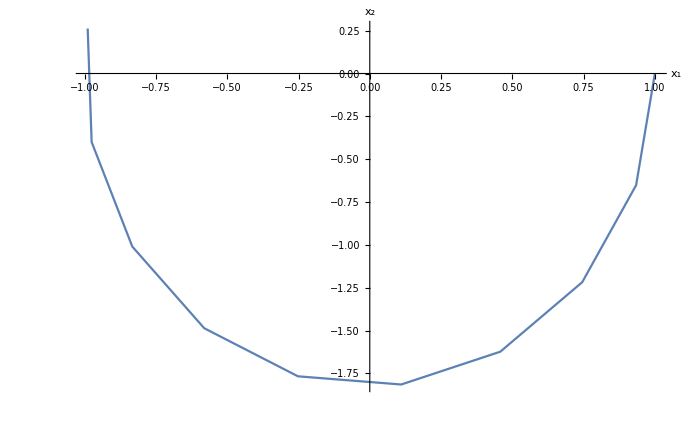

```mathematica
Show[ListLinePlot[{data},AxesLabel->{"x_1","x_2"},AxesStyle->Thick,LabelStyle->Directive[20]]]
```